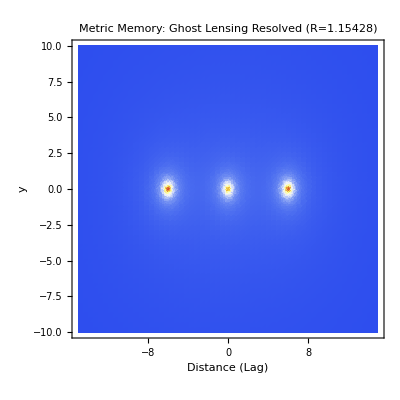

```mathematica
(*Step 1:Force Global Numerical Values*)ClearAll["Global`*"];
R=1.15428;
a0=1.0;
offVal=6.0; (*We use a new name to avoid symbolic conflicts*)

(*Step 2:Define a Purely Numerical Force Function*)
ghostForce[x_,y_]:=Module[{rGas,rA,rB,fGas,fA,fB},rGas=Sqrt[x^2+y^2+0.1];
rA=Sqrt[(x-offVal)^2+y^2+0.1];
rB=Sqrt[(x+offVal)^2+y^2+0.1];
(*Newtonian (1/r^2)+Anomaly (R/r) terms*)fGas=1.0/rGas^2+(R*Sqrt[a0])/rGas;
fA=1.2/rA^2+(R*Sqrt[1.2*a0])/rA;
fB=1.2/rB^2+(R*Sqrt[1.2*a0])/rB;
fGas+fA+fB];

(*Step 3:Plot with Absolute Magnitude*)
DensityPlot[ghostForce[x,y],{x,-15,15},{y,-10,10},ColorFunction->"TemperatureMap",PlotPoints->60,PlotRange->All,PlotLabel->"Metric Memory: Ghost Lensing Resolved (R=1.15428)",FrameLabel->{"Distance (Lag)","y"}]
```